```mathematica
Solve[a==a/(1-a*b)&&b==0.25,{a}]
```

{}

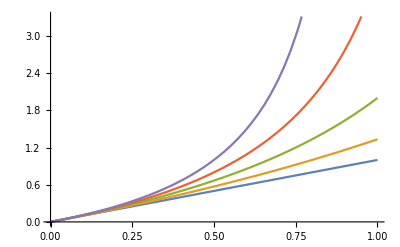

```mathematica
Plot[Evaluate@Table[a/(1-a*b)/.b->bb,{bb,0,1,0.25}],{a,0,1}]
```

Power::infy: Infinite expression 1/0. encountered.

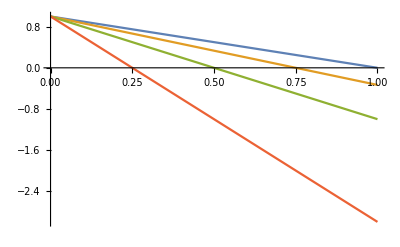

```mathematica
Plot[Evaluate@Table[(1-b-a)/(1-b)/.b->bb,{bb,0,1,0.25}],{a,0,1}]
```

```mathematica
f[a_,b_]:=a/(1-a*b)
f[]
```

```mathematica
For[t=0.25;k=1,k≤10000,k++,t=(t/(1-t*0.9))*2];Print[t]
```

-1.11111

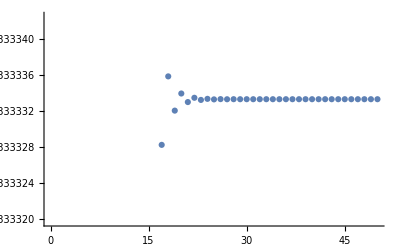

```mathematica
initialCfp=0.02;cv=0.5;
conc={};For[cfp=0.02;i=1,i≤50,i++,cfp=initialCfp-cv*cfp;AppendTo[conc,cfp]]
ListPlot@conc
```

```mathematica
;
```

```mathematica
initialCfp=0.02;cv=0.01;
conc={};For[cfp=0.02;i=1,i≤500,i++,cfp=initialCfp-cv*cfp];AppendTo[conc,cfp]
```

{0.019802}

```mathematica
conc={};Table[For[cfp=0.02;i=1,i≤500,i++,cfp=k-cv*cfp];AppendTo[conc,cfp],{k,0.001,0.02,0.001}][[-1]]
```

{0.000990099,0.0019802,0.0029703,0.0039604,0.0049505,0.00594059,0.00693069,0.00792079,0.00891089,0.00990099,0.0108911,0.0118812,0.0128713,0.0138614,0.0148515,0.0158416,0.0168317,0.0178218,0.0188119,0.019802}

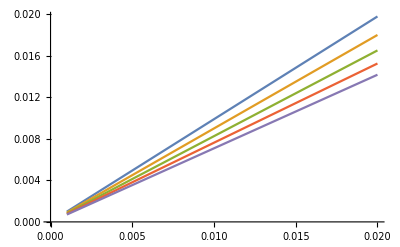

```mathematica
data=Table[Table[conc={};{k,For[cfp=0.02;i=1,i≤500,i++,cfp=k-j*cfp];AppendTo[conc,cfp][[1]]},{k,0.001,0.02,0.001}],{j,0.01,0.5,0.1}];
ListLinePlot@data
```

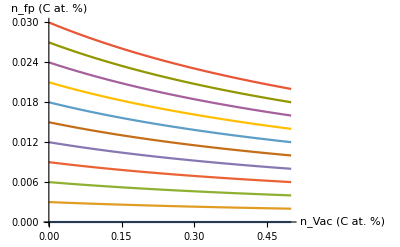

```mathematica
data=Table[Table[conc={};{j,For[cfp=0.02;i=1,i≤500,i++,cfp=k-j*cfp];AppendTo[conc,cfp][[1]]},{j,0.00,0.5,0.02}],{k,0.00,0.03,0.003}];
ListLinePlot[data,AxesLabel->{"n_Vac (C at. %)","n_fp (C at. %)"}]
```

```mathematica
data=Table[Table[conc={};{j,For[cfp=0.02;i=1,i≤500,i++,cfp=k-j*cfp];AppendTo[conc,cfp][[1]]},{j,0.00,0.5,0.02}],{k,0.00,0.03,0.003}];
ListLinePlot[data,AxesLabel->{"n_Vac (C at. %)","n_fp 33(C at. %)"}]
```

```mathematica
plotOptions={AspectRatio->0.66,FrameLabel->{Style["n_vac (at. %) ",20,Black],Style["n_fp (at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,{1.3,3.3}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Black,Dashing[0.03]],ImageSize->6000,PlotLegends->Placed[{Style["Bound",18]},{0.83,0.93}]};
plotOptions2={AspectRatio->0.66,FrameLabel->{Style["n_vac (at. %) ",20,Black],Style["n_fp (at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,Automatic},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Red],ImageSize->600,PlotLegends->Placed[{Style["Unbound",18]},{0.83,0.83}]};
```

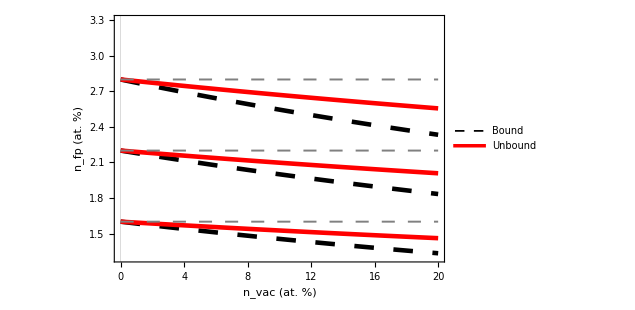

```mathematica
p1=Plot[{Evaluate@Table[100*i/(1+x/100),{i,0.01,0.03,0.006}]},{x,0,20},Evaluate@plotOptions];
p2=Plot[{Evaluate@Table[100*i/(1+x/100)^0.5,{i,0.01,0.03,0.006}]},{x,0,20},Evaluate@plotOptions2];
p3=Plot[{Table[100*i,{i,0.01,0.03,0.006}]},{x,0,20},PlotStyle->Directive[Gray,Dashing[0.02],Thickness[0.003]]];
frenkvsvac=Show[{p1,p2,p3}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Notes-post-doc/images/frenkel-conc-vs-vac-conc.pdf",frenkvsvac]
```

/Users/tom/Documents/Lyx_documents/Notes-post-doc/images/frenkel-conc-vs-vac-conc.pdf

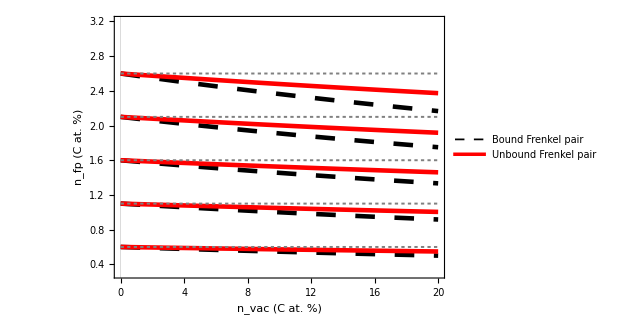

```mathematica
plotOptions3={AspectRatio->0.7,FrameLabel->{Style["n_vac (C at. %) ",20,Black],Style["n_fp (C at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,{0.3,3.2}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Black,Dashing[0.03]],ImageSize->6000,PlotLegends->Placed[{Style["Bound Frenkel pair",18]},{0.71,0.93}]};
plotOptions4={AspectRatio->0.7,FrameLabel->{Style["n_vac (C at. %) ",20,Black],Style["n_fp (C at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,Automatic},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Red],ImageSize->600,PlotLegends->Placed[{Style["Unbound Frenkel pair",18]},{0.71,0.83}]};

q1=Plot[{Evaluate@Table[100*i/(1+x/100),{i,0.001,0.03,0.005}]},{x,0,20},Evaluate@plotOptions3];
q2=Plot[{Evaluate@Table[100*i/(1+x/100)^0.5,{i,0.001,0.03,0.005}]},{x,0,20},Evaluate@plotOptions4];
q3=Plot[{Table[100*i,{i,0.001,0.03,0.005}]},{x,0,20},PlotStyle->Directive[Gray,Dashing[0.005],Thickness[0.003]]];
frenkvsvac2=Show[{q1,q2,q3}]
```

```mathematica
0.27/1.69
1/6//N
```

0.159763

0.166667

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkel-conc-vs-vac-conc.pdf",frenkvsvac2]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkel-conc-vs-vac-conc.pdf

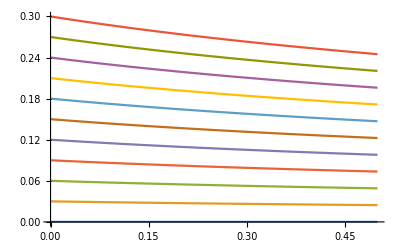

```mathematica
Plot[Evaluate@Table[i/(1+x)^0.5,{i,0,0.3,0.03}],{x,0,0.5}]
```

```mathematica
1/(1-0.02)
```

1.02041